# Pound-Drever-Hall Error Signal Derivation

## Derivation of PDH error signal, following March 18, 2026 tutorial here: https://ccahilla.github.io/lasers-and-optomechanics/tutorials/

#### 0. Fabry Perot cavity reflection as a function of phase

```mathematica
refl[ϕ_]:=(r1-r2 Exp[-I 2ϕ])/(1-r1 r2 Exp[-I 2ϕ]);
```

#### 1. What is the total electric field incident on the front of the cavity?

Carrier input

```mathematica
Ein=E0 Exp[I ω0 t];
```

Carrier + Upper Sideband + Lower Sideband

```mathematica
Eintotal=Ein(1+I Γ/2 Exp[I Ω t]+I Γ/2 Exp[-I Ω t])
```

ⅇ^(ⅈ t ω0) E0 (1+1/2 ⅈ ⅇ^(-ⅈ t Ω) Γ+1/2 ⅈ ⅇ^(ⅈ t Ω) Γ)

#### 2. Write down three single-pass phases ϕ0 , ϕusb , ϕlsb that the carrier, upper sideband, and lower sideband, will experience as they traverse the cavity, in terms of the cavity length L, and carrier and RF frequencies ω0 and Ω.

Where L is the nominal cavity length:

```mathematica
params={ϕ0->(ω0 L)/c,ϕusb->((ω0+Ω)L)/c,ϕlsb->((ω0-Ω)L)/c};
```

I have make this a list of parameters, so we can leave things in terms of ϕ0,ϕusb,ϕlsb,
Notice that we can also do another phase breakdown where 

ϕusb = ϕ0 + ϕrf and ϕlsb = ϕ0 - ϕrf
where
ϕrf = (Ω L)/c.

#### 3. Write down the cavity total reflected field Erefl in terms of the reflection function r(ϕ) and ϕ0 , ϕusb , ϕlsb

r0 is the reflected carrier refl[ϕ0],
rpΩ is the reflected upper sideband refl[ϕusb],
rmΩ is the reflected lower sideband refl[ϕlsb].

```mathematica
reflparams={r0->refl[ϕ0],rpΩ->refl[ϕusb],rmΩ->refl[ϕlsb]};
```

```mathematica
Erefltotal=Ein(r0+I Γ/2 rpΩ Exp[I Ω t]+I rmΩ Γ/2 Exp[-I Ω t]);
```

#### 4. Write down the cavity total reflected power P_refl (t) in terms of the reflection function r(ϕ) and ϕ0 , ϕusb , ϕlsb .

Use ComplexExpand, which assumes all variables are real variables, with Conjugate to quickly calculate our power.
However, in Mathematica we need to be careful because r0, rusb, and rlsb are NOT real variables, they are complex.
So when we take the complex conjugate we need to keep track of them.

I keep track of this manually below, by replacing r0, rusb, and rlsb with r0c, rusbc, and rlsbc, where the “c” suffix indicates complex conjugate.  
Not elegant but it works.

TrigToExp expands our trig expressions we get from FullSimplify into exponentials, which is easier to reach given our starting point

```mathematica
reflcparams={r0c->refl[-ϕ0],rpΩc->refl[-ϕusb],rmΩc->refl[-ϕlsb]};
```

```mathematica
Erefltotalc=TrigToExp[ComplexExpand[Conjugate[Erefltotal]]]/.{r0->r0c,rpΩ->rpΩc,rmΩ->rmΩc}
```

ⅇ^(-ⅈ t ω0) E0 r0c-1/2 ⅈ ⅇ^(ⅈ t Ω-ⅈ t ω0) E0 rmΩc Γ-1/2 ⅈ ⅇ^(-ⅈ t Ω-ⅈ t ω0) E0 rpΩc Γ

```mathematica
Prefltotal=TrigToExp[FullSimplify[ComplexExpand[Erefltotal Erefltotalc]]]
```

E0^2 r0 r0c+1/2 ⅈ ⅇ^(-ⅈ t Ω) E0^2 r0c rmΩ Γ-1/2 ⅈ ⅇ^(ⅈ t Ω) E0^2 r0 rmΩc Γ+1/2 ⅈ ⅇ^(ⅈ t Ω) E0^2 r0c rpΩ Γ-1/2 ⅈ ⅇ^(-ⅈ t Ω) E0^2 r0 rpΩc Γ+1/4 E0^2 rmΩ rmΩc Γ^2+1/4 ⅇ^(2 ⅈ t Ω) E0^2 rmΩc rpΩ Γ^2+1/4 ⅇ^(-2 ⅈ t Ω) E0^2 rmΩ rpΩc Γ^2+1/4 E0^2 rpΩ rpΩc Γ^2

```mathematica
Prefltotal=Prefltotal/.{Γ^2->0}
```

E0^2 r0 r0c+1/2 ⅈ ⅇ^(-ⅈ t Ω) E0^2 r0c rmΩ Γ-1/2 ⅈ ⅇ^(ⅈ t Ω) E0^2 r0 rmΩc Γ+1/2 ⅈ ⅇ^(ⅈ t Ω) E0^2 r0c rpΩ Γ-1/2 ⅈ ⅇ^(-ⅈ t Ω) E0^2 r0 rpΩc Γ

#### 5. Set the coefficient for e^(-i Ω t) equal to some complex number z, and the coefficient for e^(i Ω t) equal to y. What is z and y? Is there any connection between z and y? What is it?

First, Collect our P_refl(t) by using e^(-i Ω t) and e^(i Ω t) coefficients.

```mathematica
Collect[Prefltotal,{ⅇ^(ⅈ t Ω),ⅇ^(-ⅈ t Ω)}]
```

E0^2 r0 r0c+ⅇ^(ⅈ t Ω) (-1/2 ⅈ E0^2 r0 rmΩc Γ+1/2 ⅈ E0^2 r0c rpΩ Γ)+ⅇ^(-ⅈ t Ω) (1/2 ⅈ E0^2 r0c rmΩ Γ-1/2 ⅈ E0^2 r0 rpΩc Γ)

The first term above is the DC term, the second term associated with ⅇ^(ⅈ t Ω) is the y term, and the third term associated with ⅇ^(-ⅈ t Ω) is the z term:

```mathematica
z=Simplify[(1/2 ⅈ E0^2 r0c rmΩ Γ-1/2 ⅈ E0^2 r0 rpΩc Γ)]
y=Simplify[(-1/2 ⅈ E0^2 r0 rmΩc Γ+1/2 ⅈ E0^2 r0c rpΩ Γ)]
```

1/2 ⅈ E0^2 (r0c rmΩ-r0 rpΩc) Γ

-1/2 ⅈ E0^2 (r0 rmΩc-r0c rpΩ) Γ

Analyzing z and y we see that y is the complex conjugate of z.  
We can write y = z^*.

#### 6. Rewrite P_refl in terms of z and y.

Prefl=E0^2 r0 r0c+z^* ⅇ^(ⅈ t Ω) +z ⅇ^(-ⅈ t Ω)

#### 7. P_I + i P_Q = P^Ω . Show we can rewrite the demodulation in this way.

Cos[Ωt]+i Sin[Ωt] = e^(i Ω t), so we can combine our two real demodulations into a single complex demodulation.  This will gives us a complex number whose real and imaginary parts represent our usual I and Q outputs.

#### 8. Calculate the 1Ω demodulated power P_refl^Ω(ϕ0, ϕ usb , ϕlsb). What can we see pops out?

Looking at our Prefl expression above:
Prefl=E0^2 r0 r0c+z^* ⅇ^(ⅈ t Ω) +z ⅇ^(-ⅈ t Ω) 
it’s clear that if we multiply by e^(i Ω t) and integrate Prefl by one cycle in Ωt, the DC term and ⅇ^(ⅈ t Ω) will go to ⅇ^(ⅈ t Ω) and ⅇ^(2ⅈ t Ω), and will integrate to zero over one cycle.

BUT the ⅇ^(-ⅈ t Ω) term goes to stationary in time, so we should get exactly z out of our demodulation:
P_refl^Ω = z.

```mathematica
PreflΩ=z
```

1/2 ⅈ E0^2 (r0c rmΩ-r0 rpΩc) Γ

#### 9. Calculate the derivative of P_refl^Ω with respect to ϕ0, then evaluate it about zero.

#### 10. Plot the real and imaginary parts of P_refl^Ω(ϕ_0, ϕusb, ϕlsb ) as a function of ϕ0 ∈ [−π, π].

```mathematica
values={L->1,T1->0.1,T2->0.1,r1->√(1-T1),r2->√(1-T2),
E0->1,Γ->0.1,ϕusb->ϕ0+π/4,ϕlsb->ϕ0-π/4}
```

{L→1,T1→0.1,T2→0.1,r1→√(1-T1),r2→√(1-T2),E0→1,Γ→0.1,ϕusb→π/4+ϕ0,ϕlsb→-π/4+ϕ0}

```mathematica
PreflΩ/.reflparams/.reflcparams
```

1/2 ⅈ E0^2 (((r1-ⅇ^(2 ⅈ ϕ0) r2) (r1-ⅇ^(-2 ⅈ ϕlsb) r2))/((1-ⅇ^(2 ⅈ ϕ0) r1 r2) (1-ⅇ^(-2 ⅈ ϕlsb) r1 r2))-((r1-ⅇ^(-2 ⅈ ϕ0) r2) (r1-ⅇ^(2 ⅈ ϕusb) r2))/((1-ⅇ^(-2 ⅈ ϕ0) r1 r2) (1-ⅇ^(2 ⅈ ϕusb) r1 r2))) Γ

```mathematica
plotPreflΩ=PreflΩ/.reflparams/.reflcparams//.values
```

(0.+0.05 ⅈ) (((0.948683-0.948683 ⅇ^(2 ⅈ ϕ0)) (0.948683-0.948683 ⅇ^(-2 ⅈ (-π/4+ϕ0))))/((1-0.9 ⅇ^(2 ⅈ ϕ0)) (1-0.9 ⅇ^(-2 ⅈ (-π/4+ϕ0))))-((0.948683-0.948683 ⅇ^(-2 ⅈ ϕ0)) (0.948683-0.948683 ⅇ^(2 ⅈ (π/4+ϕ0))))/((1-0.9 ⅇ^(-2 ⅈ ϕ0)) (1-0.9 ⅇ^(2 ⅈ (π/4+ϕ0)))))

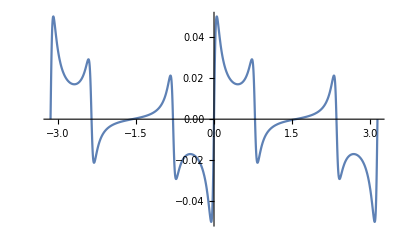

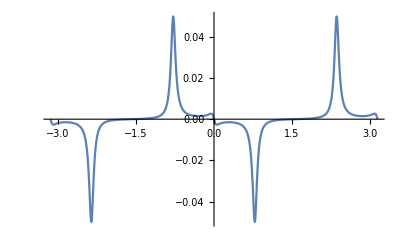

```mathematica
Plot[Re[plotPreflΩ],{ϕ0,-π,π},PlotRange->Full]
Plot[Im[plotPreflΩ],{ϕ0,-π,π},PlotRange->Full]
```